```mathematica
areaOfDetector=(19/1000)^2; (* 19mm x 19mm *)
areaOfAperture=(16*(4+Pi))/1000^2; (*8mm x 16mm with rounded edges *)
detectorFieldOfViewDiameter=2*Degree;
detectorFieldOfViewSolidAngle=2*Pi*(1-Cos[detectorFieldOfViewDiameter/2])
```

2 π (1-Cos[°])

```mathematica
irradianceFilename="E:\\\\Repositories\\github\\MitsubaARCF\\arcf-model\\arcf-irradiance.m";
radianceFilename="E:\\\\Repositories\\github\\MitsubaARCF\\arcf-model\\arcf-radiance.m";
```

```mathematica
irradianceFilename="/home/sidney/Repositories/github/MitsubaARCF/arcf-model/arcf-irradiance.m";
radianceFilename="/home/sidney/Repositories/github/MitsubaARCF/arcf-model/arcf-radiance.m";
```

```mathematica
Get[irradianceFilename];
irradiance=data;
signalIrradiance=Mean[Flatten[irradiance]]
```

0.316398

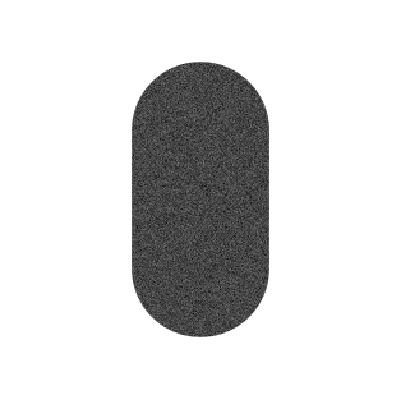

-Graphics3D-

-Graphics3D-

```mathematica
ArrayPlot[irradiance,PlotRange->All]
ListPlot3D[irradiance,PlotRange->All]
ListPlot3D[LowpassFilter[irradiance,1/10],PlotRange->All]
```

```mathematica
(* This should be equal to the W/m^2 of the emitter. *)
signalIrradiance*areaOfDetector/areaOfAperture
```

0.999598

```mathematica
Get[radianceFilename];
radiance=data;
signalRadiance=Mean[Flatten[radiance]]
```

6.04079×10^-12

```mathematica
ArrayPlot[radiance]
ListPlot3D[radiance,PlotRange->All]
ListPlot3D[LowpassFilter[radiance,1/5],PlotRange->All]
```

-Graphics-

-Graphics3D-

-Graphics3D-

```mathematica
bsdfPerfect=N[1/Pi,30]
bsdfEstimate=(signalRadiance/signalIrradiance)/detectorFieldOfViewSolidAngle
```

0.318309886183790671537767526745

1.99511×10^-8

```mathematica
bsdfEstimate/bsdfPerfect
```

2.21189